# 05/06/2024 - In Class Demo

## Physics 3400 / Math 3440 - Spring Quarter 2024

## Nullcline Examples

### Example #1

Let’s begin by considering the following system.  

ẋ = y
ẏ =2 - y - sin(x),   x∈[0,2π), y∈ℝ

Let’s plot the phase-plane along with the nullclines.  Here, the x-nullcline is given by y = 0, and the y nullcline is given by y = 2 - sin(x).

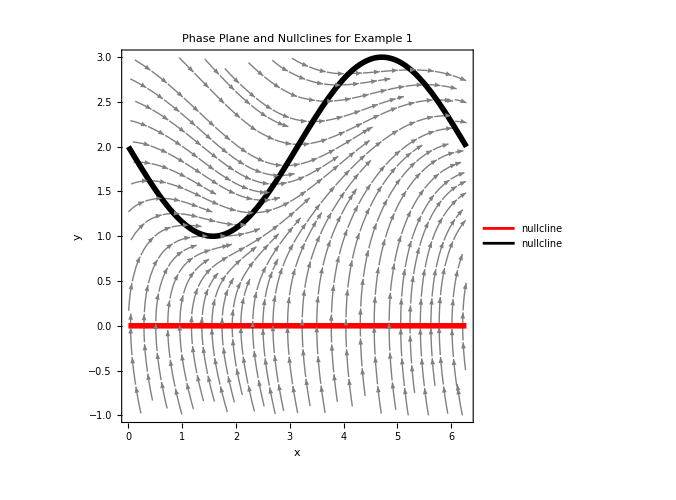

```mathematica
f1[x_,y_] = y;
g1 [x_,y_]= 2 - y - Sin[x];
p1=StreamPlot[{f1[x,y],g1[x,y]},{x,0,2π},{y,-1,3},
ImageSize->500,
StreamColorFunction->None,
StreamStyle->Gray,
StreamPoints->60,
StreamScale->0.05];
p2=Plot[{0,2-Sin[x]},{x,0,2π},
PlotStyle->{
{Red,Thickness->0.008},
{Black,Thickness->0.008}
},
PlotLegends->{
" nullcline",
" nullcline"
}];
Show[p1,p2,
FrameLabel->{"x","y"},
PlotLabel->"Phase Plane and Nullclines for Example 1"]
```

### Example #2

Now, let’s consider the system given by 

ẋ = x^2-1
ẏ =a(x^2-1) - x y,                     x,y∈ℝ, a≥0.

We can construct a manipulate to plot the phase plane and nullclines as we vary the parameter a.
Here, the x-nullclines are given by x = ±1, and the y-nullclines are given by  y = 0, x = 0 if a = 0, or y = a(x^2-1)/x if a>0.  
However, we can simply use “ContourPlot” in Mathematica with the restrictions that f==0 to give the x-nullclines, and g==0 to give the y-nullclines.

```mathematica
f2[x_,y_] = x^2-1;
g2[x_,y_,a_] = a(x^2-1) - x y;
eqPts = Solve[{f2[x,y]==0,g2[x,y,a]==0},{x,y}];

Manipulate[
p1=StreamPlot[{f2[x,y],g2[x,y,a]},{x,-2,2},{y,-2,2},
ImageSize->500,
StreamColorFunction->None,
StreamStyle->Gray,
StreamPoints->40,
StreamScale->0.05];
(*Note: this is the trick mentioned above.  That is, rather than solving for the nullclines specifically, we can use ContourPlot to plot precisely when f(x,y) = 0.*)
p2 = ContourPlot[{f2[x,y]==0,g2[x,y,a]==0},{x,-2,2},{y,-2,2},
ContourStyle->{
{Thickness[.008],ColorData["SolarColors"][.8]},
{Thickness[.008],ColorData["SolarColors"][.2],Dashed}},
PlotLegends->{
"x nullcline",
"y nullcline"}
];

eqPtsPlot = ListPlot[{x,y}/.eqPts,
PlotMarkers->{Automatic,Scaled[.02]},
PlotStyle->Black];

Show[p1,p2,eqPtsPlot,PlotRange->{-2,2},FrameLabel->{"x","y"},PlotLabel->"Phase Plane and Nullclines for Example 2"],

{{a,0},-.2,.2}] 

(* Note: by defining the range of "a" in the Manipulate as {{a,0},-.2,.2}, we are saying let "a" range from a = -.2 to a = +.2 but start with the default value of a = 0.  *)
```